## Prices: gbmp and curPrice

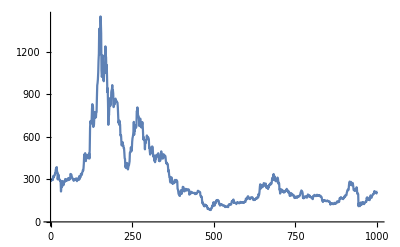

GeometricBrownianMotionProcess[0.00115444,0.0545733,212.091]

```mathematica
Import["https://api.coingecko.com/api/v3/coins/ethereum/market_chart?vs_currency=usd&days=1000","json"];
First[%][[2]];
ethPrices=Transpose[%][[2]];
initPrice=Last[ethPrices];
ListLinePlot[ethPrices,PlotRange->All]
FindProcessParameters[ethPrices,GeometricBrownianMotionProcess[μ,σ,s0]];
gbmp=GeometricBrownianMotionProcess[μ,σ,initPrice]/.%
```

## Monte Carlo: finalPriceMC

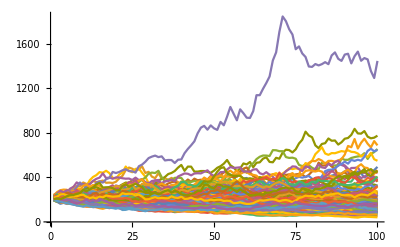

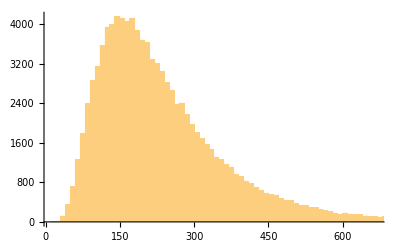

```mathematica
daysMC=100;
trialsMC=100000;

(* Small 100 trial visualization *)
ListLinePlot[RandomFunction[gbmp,{1,daysMC,1},100],PlotRange->All]

runsMC=RandomFunction[gbmp,{1,daysMC,1},trialsMC];
finalPriceMC=Sort[runsMC["SliceData",daysMC]];
Histogram[%,{10}]
```

## RB Coin: Statistics

```mathematica
targetUSD=1;
initialMargin=0.5;

collateralETH =((1+initialMargin)*targetUSD)/initPrice;
collateralUSD=collateralETH*initPrice;
initPriceBlackETH=(collateralETH-targetUSD/initPrice);

(* Print Statements *)
Print["Stability target is $",targetUSD, " USD."];
Print["That is ", targetUSD/initPrice, " ETH at the current exchange rate of ",initPrice," USD/ETH."];
Print["Over-collaterialzing by ",initialMargin,  ", the contract holds ",collateralETH ," ETH (worth $",collateralUSD," USD)."];
Print["The break-even exchange rate is ",targetUSD/collateralETH," ETH/USD"]
```

Stability target is $1 USD.

That is 0.00471495 ETH at the current exchange rate of 212.091 USD/ETH.

Over-collaterialzing by 0.5, the contract holds 0.00707243 ETH (worth $1.5 USD).

The break-even exchange rate is 141.394 ETH/USD

## RB Coin: Charts

```mathematica
EvaluateRB [targetUSD_,initialMargin_,curPrice_,finalPriceMC_]:=
Module[{collateralETH,bvalue,evalRB},

collateralETH=((1+initialMargin)*targetUSD)/curPrice;

bvalue[exrate_]:=collateralETH*exrate-targetUSD;

evalRB[exrate_]:=If[bvalue[exrate]<0,
{collateralETH*exrate,0},
{targetUSD,bvalue[exrate]}];

Transpose[evalRB/@finalPriceMC]
]

{finalPriceRed,finalPriceBlack}=EvaluateRB[1,0.5,initPrice,finalPriceMC];

ddd1={finalPriceMC,finalPriceRed}//Transpose;
ddd2={finalPriceMC,finalPriceBlack}//Transpose;
ddd3={finalPriceMC,initPriceBlackETH*finalPriceMC}//Transpose;

lll[price_]:=Line[{{price,0},{price,Max[finalPriceBlack]}}];
l1=lll[initPrice];
l2=lll[targetUSD/collateralETH];
legend={"Red Coin","Black Coin","ETH"};
ListLinePlot[{ddd1,ddd2,ddd3},Epilog->{Dashed,l1,l2},PlotLegends->legend]
```

-Graphics-

```mathematica
{finalPriceRed,finalPriceBlack}=EvaluateRB[1,0.5,initPrice,finalPriceMC];

Mean[finalPriceRed]
Mean[finalPriceBlack]
```

0.937154

0.747307

## RB Coin: Values

0.937154

0.747307